# PROPULSION SYSTEM - CALCULATION MEMORY

## INFORMATION

## a) RACERSTAR REFERENCES

Estimated Max Rotation (rpm): EMR = Kv (rpm/V) x Max Voltage (V)

Estimated Max Potency (W): EMP = Mean Voltage (V) x Max Current (A)

MaxCurrentConsumed (A): MCC = Max Current (A) ( Rotation (rpm)/ EMR (rpm))

Internal Resistence (Ω): InternalResistenceBR2205 = Ri(maxPower,maxCurrent) = maxPower (W) /(maxCurrent^2) (A^2)

## MOTOR SELECTION

## b) RACERSTAR REFERENCES

-Graphics-

-Graphics-

-Graphics-

Anoel

-Graphics-
Marca Anoel / Flash Hobby / DYS / RCTimer
Modelo: Motor Brushless D2836/6 - 1500KV(RPM/V)
Voltagem mínima - Voltagem máxima 6 V - 16.8 V
Potência 368 W
Velocidade do motor 25200 RPM
Empuxo 1,15 kgf
Diâmetro do eixo: 4 mm
Peso 70 g

============================================================
-Graphics-
Surpass
Marca Surpass Hobby
Modelo: Motor Brushless  C2836 - 1120KV(RPM/V)
Corrente máxima: 26 A
Voltagem mínima - Voltagem máxima 7 V - 15 V
Potência 380 W
Velocidade do motor 16800 RPM
Empuxo 1,422 kgf
Diâmetro do eixo: 4 mm
Peso 67 g

## c) CALCULATIONS

```mathematica
motorWeight= 28;(*grams*)
```

Estimated Max Rotation: EMR = Kv (rpm/V) x Max Voltage (V)

```mathematica
EMR[Kv_,MaxVoltage_]:=Kv MaxVoltage(*rpm*)
```

Estimated Max Potency: EMP = Mean Voltage (V) x Max Current (A)

```mathematica
EMP[MeanVoltage_,MaxCurrent_]:=MeanVoltage MaxCurrent(*rpm*)
```

MaxCurrentConsumed: MCC(Rotation) = Max Current (A) ( Rotation (rpm)/ EMR (rpm))

```mathematica
MCC[MaxCurrent_,EstimatedMaxRotation_,Rotation_]:=MaxCurrent (Rotation/EstimatedMaxRotation)
```

```mathematica
Ri[ElecPower_,Current_]:=ElecPower/(Current^2)
```

```mathematica
EMR[2300,14.8 ]
```

34040.

```mathematica
EMP[14.8,27.6 ]
```

408.48

```mathematica
maxCurrent=27.6;(*Ampers*)
```

```mathematica
maxPower=950;(*Watt*)
```

```mathematica
InternalResistenceBR2205=Ri[maxPower,maxCurrent];
```

```mathematica
InternalResistenceBR2205
```

1.24711

## d) CALCULATIONS

```mathematica
maxCurrent=27.6;(*Ampers*)
```

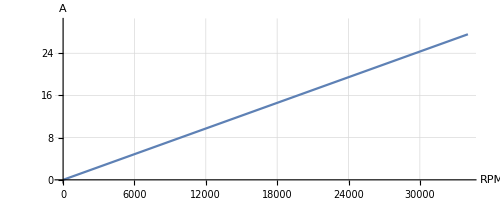

```mathematica
ParametricPlot[{Rotation,MCC[maxCurrent,EMR[2300,14.8 ],Rotation]},{Rotation, 0, EMR[2300,14.8 ]},AspectRatio->Full,PlotRange->{{0,EMR[2300,14.8 ]},{0,30}},AxesLabel->{"RPM","A"},GridLines->Automatic]
```

```mathematica
15 8
```

120

Current

## ESC SELECTION

## BATERY SELECTION

## PROPELLERS SELECTION

https://m-selig.ae.illinois.edu/props/propDB.html
-----------------------------------------------

Impementation of Gupta’s modeling

CT = (4/3 kθ[1-(1-ed).b3])-k(((k(1+k))^(0,5))-k^(0,5))[1-(1-ed).b2] ==> comparar com o dado teórico do datasheet

T = CT ρ π R.b2 (ΩR).b2 ----> T/(CTρπ R⁴) = Ω.b2

-----------------------------------------------

CT = T/(ρ π Ω.b2 R⁴) = T/(ρ n.b2 D⁴) = T/(ρ n.b2 16R⁴)
D⁴ = (2R)⁴
 D⁴ = 16R⁴ =>  ρ n.b2 16R⁴ = ρ π Ω.b2 R⁴ => n.b2 16 = π Ω.b2 => n.b2 = π Ω.b2/16 => n = (Ω.b2π/16)^(1/2)
----------------------------------------------- 
motor brushless 4S 1,5 kg 40A
motor brushless 1900kv 4s 6s
Você deve dimensionar seu multicóptero para que seja capaz de pairar no ar a apenas 50% de aceleração (ou menos), ou seja, o empuxo total gerado pelos motores a 50% deve ser maior ou igual ao peso do aparelho.

https://www.outros.net/2016/05/25/como-construir-um-drone-quadricoptero-do-zero/5/
Você deve dimensionar seu multicóptero para que seja capaz de pairar no ar a apenas 50% de aceleração (ou menos), ou seja, o empuxo total gerado pelos motores a 50% deve ser maior ou igual ao peso do aparelho.

```mathematica
ThrustModel[N1_,N2_,N3_,N4_,N5_,N6_,N7_,N8_]:=(ct ρ π (d/2)^4) (mappingY.{N1^2,N2^2,N3^2,N4^2,N5^2,N6^2,N7^2,N8^2})
```

```mathematica
NSqrd[fx_,fy_,fz_,tx_,ty_,tz_,mass_]:=(1/(ct ρ d^4)) Ycross.{fx,fy,fz-(mass 9.80665),tx,ty,tz}
```